```mathematica
NDSolve[{  x''[t]==    y[t]*(2-x[t]^2-y[t]^2),
	         y''[t]== -x[t]*(2-x[t]^2-y[t]^2), 
		x[0] ==0, y[0] ==1., x'[0]==0,y'[0]==0},
		{x,y},{t,0,30}]
```

NDSolve::ndsz: At t == 3.6524, step size is effectively zero; singularity or stiff system suspected.

{{x→InterpolatingFunction[{{0.,3.6524}},<>],y→InterpolatingFunction[{{0.,3.6524}},<>]}}

```mathematica
solve = NDSolve[{  x''[t]==    y[t]*(2-x[t]^2-y[t]^2),
	                        y''[t]== -x[t]*(2-x[t]^2-y[t]^2), 
		               x[0] ==0, y[0] ==1., x'[0]==0,y'[0]==0},
		               {x,y},{t,0,3.5}]
ParametricPlot[Evaluate[{x[t],y[t]}/.solve],{t,0,3.5}]
ParametricPlot[Evaluate[{t,x[t]       }/.solve],{t,0,3.5}]
ParametricPlot[Evaluate[{t,y[t]       }/.solve],{t,0,3.5}]
```

{{x→InterpolatingFunction[{{0.,3.5}},<>],y→InterpolatingFunction[{{0.,3.5}},<>]}}

```mathematica
График y(x)
```

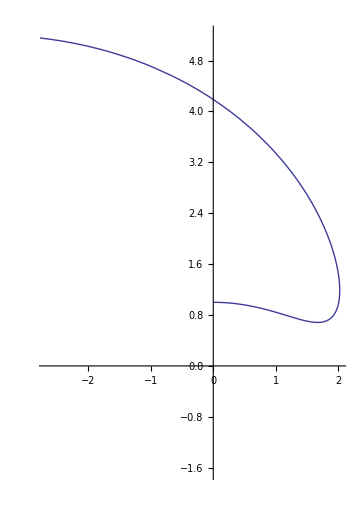

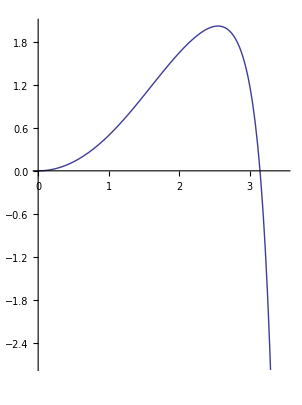

```mathematica
График x(t)
```

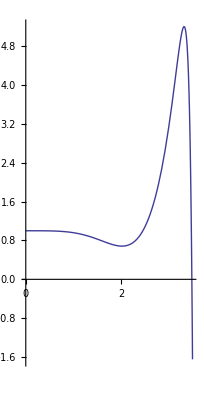

```mathematica
График y(t)
```